```mathematica
Unprotect[C,D]
```

{C,D}

### Inputing city data:

Radiation and ACEnergy Data:
The data for Radiation and ACEnergy was obtained via National Renewable Energy Laboratory (NREL) Home Page.  By simply entering the City Zip Code and data was given for the city on a monthly period.  Each city had data points for the month's radiation and the amount of ACEnergy produced from that Radiation.  The units for Solar Radiation is (kWh/m2/day) and the units for ACEnergy is (kWh).

NEW YORK (JFK AP), NY:

```mathematica
Subscript[City, 1]=NEW YORK;
```

```mathematica
Subscript[Wind, 1]={13.0,13.3,13.5,12.7,11.6,10.7,10.2,10.0,10.4,11.0,12.2,12.7};
```

```mathematica
Subscript[Radiation, 1]={3.17,4.17,4.57,5.25,5.30,5.78,5.64,5.52,5.06,4.48,2.90,2.85};
```

```mathematica
Subscript[ACEnergy, 1]={315,370,432,466,472,484,479,475,431,410,264,276};
```

PHOENIX, AZ:

```mathematica
Subscript[City, 2]=PHOENIX;
```

```mathematica
Subscript[Wind, 2]={5.3,5.8,6.6,6.9,7.0,6.7,7.1,6.6,6.3,5.8,5.3,5.1};
```

```mathematica
Subscript[Radiation, 2]={5.09,6.06,6.61,7.54,7.53,7.28,7.13,7.17,7.15,6.75,5.59,4.88};
```

```mathematica
Subscript[ACEnergy, 2]={451,486,566,613,619,559,569,576,557,566,469,438};
```

CHICAGO, IL:

```mathematica
Subscript[City, 3]=CHICAGO;
```

```mathematica
Subscript[Wind, 3]={11.6,11.4,11.8,11.9,10.5,9.3,8.4,8.2,8.9,10.1,11.1,11.0};
```

```mathematica
Subscript[Radiation, 3]={3.04,3.78,4.34,5.11,5.68,5.66,5.92,5.22,4.94,4.26,2.83,2.27};
```

```mathematica
Subscript[ACEnergy, 3]={302,336,419,455,498,470,497,444,414,389,258,220};
```

SEATTLE (SEA-TAC AP), WA

```mathematica
Subscript[City, 4]=SEATTLE;
```

```mathematica
Subscript[Wind, 4]={9.5,9.4,9.4,9.4, 8.9, 8.6, 8.1, 7.8, 8.0, 8.3, 9.1, 9.6};
```

```mathematica
Subscript[Radiation, 4]={1.54,2.50,3.71,4.37,5.31,5.52,5.88,5.17,4.98,3.00,1.76,1.26};
```

```mathematica
Subscript[ACEnergy, 4]={133,201,335,383,471,467,508,448,419,263,148,103};
```

```mathematica
Table[Subscript[EnergyValue, i]= Subscript[ACEnergy, i]*Subscript[E, cost]*dollars/(100 cents),{i,1,4}];
```

### Obtaining a function for the curves of Radiation.

The first step in analyzing the amount of energy a city can obtain from a solar panel is to analyze the amout of radiation a city recieved throughout the year.  Below is a plot of the solar radiation of a city as a function of month.

```mathematica
SolarRadiationGraph1=ListPlot[Table[Subscript[Rdata, i]=Table[{j,Subscript[Radiation, i][[j]]},{j,1,Length[Subscript[Radiation, i]]}],{i,1,4}], PlotStyle->{Red,Green,Blue,Purple},PlotRange-> {0,8},AxesLabel->{"Month","Solar Radiation"},PlotLabel->"Graphs of Solar Radiation"];
```

```mathematica
Rasterize[SolarRadiationGraph1,ImageResolution->300]
```

-Graphics-

After looking at this data, we would like to obtain a formula for the cities radiation as a function of time.  The data points seem to have a parabolic shape and therefore we will fit a parabola to the data points.  We will use the FindFit function to obtain values for the coefficients for each city.

```mathematica
Table[Subscript[sol, i]=FindFit[Subscript[Rdata, i],Subscript[a, rad,i] x^2 +Subscript[b, rad,i] x +Subscript[c, rad,i], {Subscript[a, rad,i],Subscript[b, rad,i],Subscript[c, rad,i]},{x}]
,{i,1,4}];
Table[{Subscript[a, rad,i],Subscript[b, rad,i],Subscript[c, rad,i]}={Subscript[a, rad,i],Subscript[b, rad,i],Subscript[c, rad,i]}/. Subscript[sol, i],{i,1,4}];
```

After obtianing the constants, we can define the functions below.  RadFunction is a function of the predicted amount of radiation a city may have at any given point in the year.

```mathematica
Subscript[RadFunction, 1][x_]:=Subscript[a, rad,1] x^2 +Subscript[b, rad,1] x +Subscript[c, rad,1]
Subscript[RadFunction, 2][x_]:=Subscript[a, rad,2] x^2 +Subscript[b, rad,2] x +Subscript[c, rad,2]
Subscript[RadFunction, 3][x_]:=Subscript[a, rad,3] x^2 +Subscript[b, rad,3] x +Subscript[c, rad,3]
Subscript[RadFunction, 4][x_]:=Subscript[a, rad,4] x^2 +Subscript[b, rad,4] x +Subscript[c, rad,4]
```

```mathematica
{Subscript[Color, 1],Subscript[Color, 2],Subscript[Color, 3],Subscript[Color, 4]}={Red,Green,Blue,Purple};
```

```mathematica
SolarRadiationGraph2=
Show[Table[Plot[Subscript[RadFunction, i][x],{x,0,12},PlotStyle->{Subscript[Color, i]},PlotRange-> {0,8}],{i,1,4}]];
```

We can check our Functions by plotting them with the data points.  As you may notice, the functions obtained fit the data points fairly nicely.

```mathematica
Rasterize[Show[SolarRadiationGraph1,SolarRadiationGraph2,PlotRange-> {0,8},AxesLabel->{"Month","Solar Radiation"},PlotLabel->"Graphs of Solar Radiation"],ImageResolution->300]
```

-Graphics-

### Obtaining a Function of Energy Produced by a solar panel.

We must obtain a function which converts solar radiation into actual energy produced.  We can do this by the following method:

1.  Grouping all the city data into one large set of data points.  This is done simply to obtain one set of data points which Mathematica and use to fit a single function to the conversion of radiation into the energy produced.

```mathematica
Subscript[Radiation, total]=Flatten[Table[
Table[{
Subscript[Radiation, i][[j]]},{j,1,Length[Subscript[Radiation, i]]}
],{i,1,4}]];
```

```mathematica
Subscript[ACEnergy, total]=Flatten[Table[
Table[{
Subscript[ACEnergy, i][[j]]},{j,1,Length[Subscript[ACEnergy, i]]}
],{i,1,4}]];
```

We can plot the data points in order to view how the data points behave.  This is done in order to see what type of function we would like to fit to the desired function.

```mathematica
Subscript[Points, sun vs energy, merged]=ListPlot[
LightPower=Table[{Subscript[Radiation, total][[j]],Subscript[ACEnergy, total][[j]]},{j,1,Length[Subscript[ACEnergy, total]]}],AxesLabel->{"Solar Radiation","Energy"},PlotLabel->"Graph of the Energy Produced vs Solar Radiation"];
```

```mathematica
Rasterize[Subscript[Points, sun vs energy, merged],ImageResolution->300]
```

-Graphics-

The data points look linear.  We can now fit a linear function to the data points and plot the function in order to see if the constants are justifiable.

```mathematica
Subscript[sol, solar]=FindFit[LightPower,Subscript[a, solar] x+Subscript[b, solar], {Subscript[a, solar],Subscript[b, solar]},{x}];
{Subscript[a, solar],Subscript[b, solar]}={Subscript[a, solar],Subscript[b, solar]}/. Subscript[sol, solar];
SolarFunction[x_]:=Subscript[a, solar] x+Subscript[b, solar];
```

```mathematica
Subscript[sol, solarcombined]=Show[Plot[SolarFunction[x],{x,0,8},PlotRange-> {0,600}],Subscript[Points, sun vs energy, merged],AxesLabel->{"Solar Radiation","Energy"},PlotLabel->"Graph of the Energy Produced vs Solar Radiation"];
```

```mathematica
Rasterize[Subscript[sol, solarcombined],ImageResolution->300]
```

-Graphics-

After plotting the function with the data points, we can conclude that its a fairly good fit and we can now proceed to the next step of analyzing data.

### Temperature Data for the Cities:

We must obtain formulas for the temperatures of the 4 different citys in order to calculate the efficiency of the solar panel.  This is because the efficiency of a solar panel depends on the surrounding temperatures.  After obtaining formulas of temperature with respect to time of year, we can calculate the efficiency of a solar panel at that particular time of year.

Step 1:  Importing all temperature data from the 4 cities.

```mathematica
AirportCode={KJFK,KSEA,KPHX,KORD};
```

New York City Temperatures

```mathematica
<<"Units`";
Subscript[Tempdata, 1]=WeatherData["KJFK", "MeanTemperature", {{2006, 1, 1}, {2008, 12, 31}, "Week"},"DateValue"];
Subscript[Tempdata2, 1]=Table[{(DateDifference[{2006,1,1},Subscript[Tempdata, 1][[i,1]]]/365) ,ConvertTemperature[Subscript[Tempdata, 1][[i,2]],Celsius,Fahrenheit]},{i,Length[Subscript[Tempdata, 1]]}];
```

Seattle Temperatures

```mathematica
<<"Units`";
Subscript[Tempdata, 2]=WeatherData["KSEA", "MeanTemperature", {{2006, 1, 1}, {2008, 12, 31}, "Week"},"DateValue"];
Subscript[Tempdata2, 2]=Table[{(DateDifference[{2006,1,1},Subscript[Tempdata, 2][[i,1]]]/365) ,ConvertTemperature[Subscript[Tempdata, 2][[i,2]],Celsius,Fahrenheit]},{i,Length[Subscript[Tempdata, 2]]}];
```

Arizona Temperatures

```mathematica
<<"Units`";
Subscript[Tempdata, 3]=WeatherData["KPHX", "MeanTemperature", {{2006, 1, 1}, {2008, 12, 31}, "Week"},"DateValue"];
Subscript[Tempdata2, 3]=Table[{(DateDifference[{2006,1,1},Subscript[Tempdata, 3][[i,1]]]/365) ,ConvertTemperature[Subscript[Tempdata, 3][[i,2]],Celsius,Fahrenheit]},{i,Length[Subscript[Tempdata, 3]]}];
```

Chicago Temperatures

```mathematica
<<"Units`";
Subscript[Tempdata, 4]=WeatherData["KORD", "MeanTemperature", {{2006, 1, 1}, {2008, 12, 31}, "Week"},"DateValue"];
Subscript[Tempdata2, 4]=Table[{(DateDifference[{2006,1,1},Subscript[Tempdata, 4][[i,1]]]/365) ,ConvertTemperature[Subscript[Tempdata, 4][[i,2]],Celsius,Fahrenheit]},{i,Length[Subscript[Tempdata, 4]]}];
```

```mathematica
Unprotect[C,D];
```

It is known from past experience that the function of temperature with respect to time is a Sin function.  Therefore, the temperature functions will be fit to the generic formula A+B Sin[C(x+D)].

```mathematica
Table[
Subscript[sol, i]=FindFit[Subscript[Tempdata2, i],Subscript[A, i]+Subscript[B, i] Sin[Subscript[C, i](x-Subscript[D, i])], {{Subscript[A, i],50},{Subscript[B, i],20},{Subscript[C, i],-6},{Subscript[D, i],-2}},{x}],{i,1,4}];
Table[{Subscript[A, i],Subscript[B, i],Subscript[C, i],Subscript[D, i]}={Subscript[A, i],Subscript[B, i],Subscript[C, i],Subscript[D, i]}/. Subscript[sol, i],{i,1,4}];
```

The new constants are now used to define the temperature function for a specific city, as seen below:

```mathematica
Subscript[Temperature, 1][x_]:=Subscript[A, 1]+Subscript[B, 1] Sin[Subscript[C, 1](x-Subscript[D, 1])]
Subscript[Temperature, 2][x_]:=Subscript[A, 2]+Subscript[B, 2] Sin[Subscript[C, 2](x-Subscript[D, 2])]
Subscript[Temperature, 3][x_]:=Subscript[A, 3]+Subscript[B, 3] Sin[Subscript[C, 3](x-Subscript[D, 3])]
Subscript[Temperature, 4][x_]:=Subscript[A, 4]+Subscript[B, 4] Sin[Subscript[C, 4](x-Subscript[D, 4])]
```

To ensure the functions obtained fit the data points accordinly, the function is graphed along with the data points.

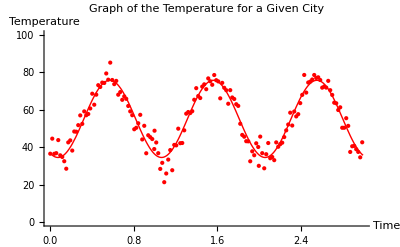

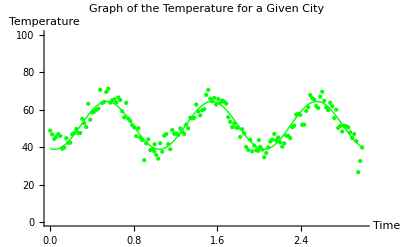

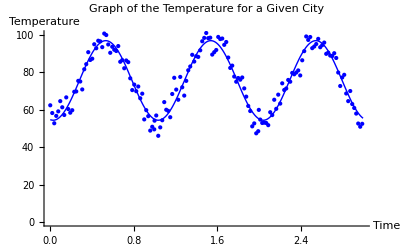

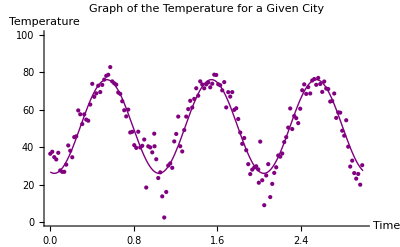

```mathematica
For[i=1,i≤4,i++,
Print[
Show[
ListPlot[Subscript[Tempdata2, i],PlotStyle->{Subscript[Color, i]}],
Plot[Subscript[A, i]+Subscript[B, i] Sin[Subscript[C, i](x-Subscript[D, i])],{x,0,3},PlotStyle->{Subscript[Color, i]}],PlotRange->{0,100},
AxesLabel->{"Time","Temperature"},PlotLabel->"Graph of the Temperature for a Given City"]]];
```

### Efficiency Function

The efficiency of a solar panel is a linear function which was found to be Efficiency = -4/9 T + 82.  This equation expressed the efficiency out of 100 rather than 1, and therefore the equation must be divided by 100.  Also, the efficiency is a function of temperature in degrees Celcius and therefore we must convert the function of temperature obtained previously from Farenheith to Celcius.  The resulting equation will look as follows:

```mathematica
Efficiency[x_] := (-(4/9)* ((x - 32)/1.8) + 82)/100;
```

### Power generated by a solar panel:

We can now combine all our formulas.  
N_solarpanels is defined to be the number of solar panels.  It will be defined as 1 in order to compare the power generated by each region.
The Solar Function is used to convert radiation into the numerical value of kWhrs produced, we must use the radiation function within the solar function in order to obtain a value for radiation which can be used in order to obtain a value for power generated by the solar panel.
The efficiency fucntion is dependant on the temperature function.  The temperature function must first calculate the temperature of the city at a certain time and once this value is obtained it will be used to calculate the efficiency of the solar panel at that particualr time in the year.

```mathematica
Subscript[N, solarpanels]=1;
```

```mathematica
Subscript[Energy, solar,1][x_]:=Subscript[N, solarpanels] SolarFunction[Subscript[RadFunction, 1][x]]*Efficiency[Subscript[Temperature, 1][x/12]]
Subscript[Energy, solar,2][x_]:=Subscript[N, solarpanels] SolarFunction[Subscript[RadFunction, 2][x]]*Efficiency[Subscript[Temperature, 2][x/12]]
Subscript[Energy, solar,3][x_]:=Subscript[N, solarpanels] SolarFunction[Subscript[RadFunction, 3][x]]*Efficiency[Subscript[Temperature, 3][x/12]]
Subscript[Energy, solar,4][x_]:=Subscript[N, solarpanels] SolarFunction[Subscript[RadFunction, 4][x]]*Efficiency[Subscript[Temperature, 4][x/12]]
```

A plot of energy output as a function of time is generated.

```mathematica
EnergyPlots=Show[
Table[
Plot[
Subscript[Energy, solar,i][x],{x,0,12},
PlotStyle->{Subscript[Color, i]},PlotRange-> {0,500}],{i,1,4}],AxesLabel->{"Months","Energy"},PlotLabel->"Energy Produced by Solar Panels"];
```

```mathematica
Rasterize[EnergyPlots,ImageResolution->300]
```

-Graphics-

### BWC Excel 10kW Class Wind Turbine:

Start-up wind speed:

```mathematica
Subscript[wind, startup]=7.5;
```

```mathematica
Subscript[Wind, speed]=Table[4.0+0.5i,{i,0,7}] ;
```

Converting units to the desired MPH.

```mathematica
Subscript[Wind, speed,MPH]=Subscript[Wind, speed]*2.24;
```

The BWC Excel 10kW Class Turbine has the following energy production based on wind speeds.

```mathematica
Subscript[Power, gen,year]={1221,1781,2443,2766,3331,3610,3877,4047};
```

Because the values are based on yearly energy production, we must divide the values by 12 in order to have them in monthly production.

```mathematica
Subscript[Power, gen,month]=N[Subscript[Power, gen,year]/12];
```

We can now couple the data into a set of data points in which we can plot and obtain a formula.

```mathematica
Subscript[Turbine, data]=Table[{Subscript[Wind, speed,MPH][[i]],Subscript[Power, gen,month][[i]]},{i,1,Length[Subscript[Power, gen,month]]}];
```

The data points seem to be of the Logorithmic form and therefore a fit to the generic formula c Log[x] +b.

```mathematica
Subscript[sol, turbinedata]=FindFit[Subscript[Turbine, data],(Subscript[c, turb]*Log[x])+Subscript[b, turb], {Subscript[c, turb],Subscript[b, turb]},{x}];
{Subscript[c, turb],Subscript[b, turb]}={Subscript[c, turb],Subscript[b, turb]}/. Subscript[sol, turbinedata];
```

The values for the coefficients have been found and now the forumla must be defined.

```mathematica
Subscript[Turbine, power][x_]:=Subscript[c, turb]*Log[x]+Subscript[b, turb]
```

The function obtained must be checked against the data points to ensure the validity of the function.

```mathematica
Rasterize[Show[Plot[Subscript[Turbine, power][x],{x,5,20}],ListPlot[Subscript[Turbine, data]],AxesLabel->{"Wind Speed, MPH","Energy"},PlotLabel->"Energy Produced versus Wind Speed"],ImageResolution->300]
```

-Graphics-

### Obtaining formulas for the projected winds of each city:

Plotting the average monthly wind speeds as a function of time for each city.

```mathematica
WindDataPlot=ListPlot[Table[Subscript[Winddata, i]=Table[{j,Subscript[Wind, i][[j]]},{j,1,Length[Subscript[Wind, i]]}],{i,1,4}], PlotStyle->{Red,Green,Blue,Purple},PlotRange-> {0,25},AxesLabel->{"Month","Wind Speed, MPH"},PlotLabel->"Graphs of Wind speed"];
```

```mathematica
Rasterize[WindDataPlot,ImageResolution->300]
```

-Graphics-

Once again, the general form of the sin function will be used to fit a line to the data points.

```mathematica
Table[
Subscript[Windsol, i]=FindFit[Subscript[Winddata, i],Subscript[A, wind,i]+Subscript[B, wind,i] Sin[Subscript[C, wind,i](x-Subscript[D, wind,i])], {Subscript[A, wind,i],Subscript[B, wind,i],Subscript[C, wind,i],Subscript[D, wind,i]},{x}],{i,1,4}];
Table[ {Subscript[A, wind,i],Subscript[B, wind,i],Subscript[C, wind,i],Subscript[D, wind,i]}= {Subscript[A, wind,i],Subscript[B, wind,i],Subscript[C, wind,i],Subscript[D, wind,i]}/. Subscript[Windsol, i],{i,1,4}];
```

The coefficients for each function has been obtained and the functions of Windspeed for each city can now be defined.

```mathematica
Subscript[WindFunction, 1][x_]:=Subscript[A, wind,1]+Subscript[B, wind,1] Sin[Subscript[C, wind,1](x-Subscript[D, wind,1])];
Subscript[WindFunction, 2][x_]:=Subscript[A, wind,2]+Subscript[B, wind,2] Sin[Subscript[C, wind,2](x-Subscript[D, wind,2])]
Subscript[WindFunction, 3][x_]:=Subscript[A, wind,3]+Subscript[B, wind,3] Sin[Subscript[C, wind,3](x-Subscript[D, wind,3])];
Subscript[WindFunction, 4][x_]:=Subscript[A, wind,4]+Subscript[B, wind,4] Sin[Subscript[C, wind,4](x-Subscript[D, wind,4])];
```

Plotting the fucntions along with the data points to ensure the vailidity of the function.

```mathematica
Rasterize[Show[WindDataPlot,Plot[Subscript[WindFunction, 1][x],{x,0,12},PlotStyle->{Subscript[Color, 1]}],Plot[Subscript[WindFunction, 2][x],{x,0,12},PlotStyle->{Subscript[Color, 2]}],Plot[Subscript[WindFunction, 3][x],{x,0,12},PlotStyle->{Subscript[Color, 3]}],Plot[Subscript[WindFunction, 4][x],{x,0,12},PlotStyle->{Subscript[Color, 4]}]],ImageResolution->300]
```

-Graphics-

Note:  The function for the wind speed of Phoenix did not fit as nicely as the other functions, but fortunately the average wind speed in each month is below 7.5 MPH which is the necessary speed required for the start up of the turbine.  And because it does not meet this requirement, Phoenix can not produce energy via wind turbines.

The data can now be combined in order to obtain formulas for the energy produced as a function of wind speed for a given city.
N_turbines is equal to the number of turbines a city has, the default value will be 1 in order to understand how each region compare.
The function Turbine_power is a function of wind speed which is denoted by WindFunction.  These functions are time dependant.

```mathematica
Subscript[N, turbines]=1
```

1

```mathematica
Subscript[Energy, wind,1][x_]:=Subscript[N, turbines]*Subscript[Turbine, power][Subscript[WindFunction, 1][x]]
Subscript[Energy, wind,2][x_]:=0
Subscript[Energy, wind,3][x_]:=Subscript[N, turbines]*Subscript[Turbine, power][Subscript[WindFunction, 3][x]]
Subscript[Energy, wind,4][x_]:=Subscript[N, turbines]*Subscript[Turbine, power][Subscript[WindFunction, 4][x]]
```

```mathematica
WindEnergyPlots=Show[
Table[
Plot[
Subscript[Energy, wind,i][x],{x,0,12},
PlotStyle->{Subscript[Color, i]},PlotRange-> {0,300}],{i,1,4}],AxesLabel->{"Month","Energy"},PlotLabel->"Energy Produced by Wind Turbine"];
```

```mathematica
Rasterize[WindEnergyPlots,ImageResolution->300]
```

-Graphics-

### Combining the solar panel function with the wind turbine function:

```mathematica
Subscript[Energy, total,1][x_]:=Subscript[Energy, solar,1][x]+Subscript[Energy, wind,1][x]
Subscript[Energy, total,2][x_]:=Subscript[Energy, solar,2][x]+Subscript[Energy, wind,2][x]
Subscript[Energy, total,3][x_]:=Subscript[Energy, solar,3][x]+Subscript[Energy, wind,3][x]
Subscript[Energy, total,4][x_]:=Subscript[Energy, solar,4][x]+Subscript[Energy, wind,4][x]
```

```mathematica
EnergyPlots=Show[
Table[
Plot[
Subscript[Energy, total,i][x],{x,0,12},
PlotStyle->{Subscript[Color, i]}],{i,1,4}]];
```

```mathematica
Rasterize[Show[EnergyPlots,PlotRange->{0,600},AxesLabel->{"Month","Energy"},PlotLabel->"Total Energy Produced by Solar Panel and Wind Turbine"],ImageResolution->300]
```

-Graphics-

### Calculating the area under the curve.

The area under the curve is used in order to obtain the total yearly power production.  The Integrate command of Mathematica was not working properly, so the Monte Carlo method of finding area is used.

```mathematica
dots=5000;
```

```mathematica
RandomPoints=Table[{Subscript[x, i]=RandomReal[{0,12}],Subscript[y, i]=RandomReal[{0,600}]},{i,1,dots}];
```

```mathematica
RandomPointsPlot=ListPlot[RandomPoints];
```

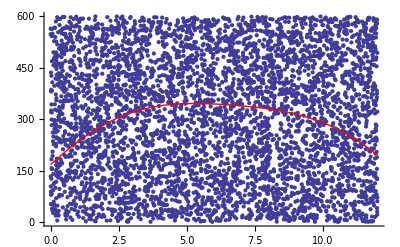

```mathematica
Show[RandomPointsPlot,Plot[
Subscript[Energy, solar,1][x],{x,0,12},PlotStyle->{Thick,Red}]]
```

We can calculate the areas under the curve of the solar panels to see how much energy we are producing in each city per year.

```mathematica
SolarArea=Table[Total[Table[{
If[Subscript[y, i]<Subscript[Energy, solar,j][Subscript[x, i]],1,0]},{i,1,dots}]],{j,1,4}
];
```

We can calculate the areas under the curve of the wind turbines to see how much energy we are producing in each city per year.

```mathematica
WindArea=Table[Total[Table[{
If[Subscript[y, i]<Subscript[Energy, wind,j][Subscript[x, i]],1,0]},{i,1,dots}]],{j,1,4}
];
```

Total Yearly Solar Energy Saved:

```mathematica
TYSES=N[(12*600)*(SolarArea/dots)];
```

Total Yearly Wind Energy Saved:

```mathematica
TYWES=N[(12*600)*(WindArea/dots)];
```

Cost of kWh for each state, [cents/ kWh]:

```mathematica
Cost={15.22,8.47,7.91,7.20};
```

Savings for each state:

```mathematica
SolarSavings=Cost*TYSES/100;
```

```mathematica
WindSavings=Cost*TYWES/100;
```

The values in the table below are for 1 solar panel and 1 wind turbine, these savings are per year.

```mathematica
Rasterize[TableForm[Table[{Subscript[City, i],SolarSavings[[i]],WindSavings[[i]]},{i,1,4}],
TableHeadings->{None,{"City","Solar Savings, USD", "Wind Savings, USD"}}],ImageResolution->300]
```

-Graphics-

Lets see how much a company in NYC can save with a range of solar panels and a range of wind turbines.  The maximum amout of solar panels are 12 and the maximum amount of wind turbines are 10.

```mathematica
Rasterize[TableForm[Table[
Table[{i*SolarSavings[[1]]+j*WindSavings[[1]]},{i,1,12}],{j,1,10}],
TableHeadings->{{"1","2","3","4","5","6","7","8","9","10"},{"1","2","3","4","5","6","7","8","9","10","11","12"}}],ImageResolution->300]
```

-Graphics-

From the chart one may notice how a company in nyc can save a maximum of roughtly $10,400 per year.